```mathematica
Res={{0.,0.5,13.918050426857521,48.713176494001324,0.06877545674077629,0.,0.,0.,0.},{0.049999999999999996,0.5,13.875151380550202,48.563029831925704,0.06875384833960012,0.0013330290656850493,0.0015268494416546352,0.0007191038696255678,0.0007293356341705785},{0.09999999999999999,0.5,13.746622414294269,48.11317845002994,0.0687692883846311,0.005420134097956948,0.006139816624187086,0.002941682917772262,0.002975790724781533},{0.15,0.5,13.532967189230053,47.36538516230519,0.0687378587900406,0.012195499055166101,0.013545519674799073,0.006658433554516699,0.006732410909737017},{0.19999999999999998,0.5,13.235022058068415,46.322577203239454,0.06873586814078174,0.022141207169445863,0.023883704929086404,0.012177468824711877,0.01230006594679905},{0.24999999999999997,0.5,12.853950586583156,44.98882705304105,0.0687449477800157,0.03500027032910163,0.036323255335046684,0.01937634068212484,0.01954596645317903},{0.3,0.5,12.39123392373774,43.36931873308209,0.06874286761915843,0.051745492528227105,0.05098230611200958,0.02873665968353578,0.028954704500044108},{0.35,0.5,11.848654368456751,41.47029028959863,0.06873516552919419,0.07282399768242676,0.0670550085099613,0.04027593672680587,0.04054134398953417},{0.39999999999999997,0.5,11.22826739102695,39.29893586859433,0.06873109148107313,0.10020676867175204,0.08442059889180392,0.054541900875467675,0.054821378303714724},{0.44999999999999996,0.5,10.53235343115017,36.863237009025596,0.06873873181724925,0.13655057438543353,0.10210878183652772,0.07153383179227725,0.07181361679582085},{0.49999999999999994,0.5,9.763332922360668,34.17166522826234,0.06868039614547385,0.1899004589569202,0.11993613271296466,0.09199168033297225,0.09223424118131718},{0.5499999999999999,0.5,8.923611145519292,31.232639009317523,0.06868486105820767,0.2891030788024757,0.13782513752974251,0.11760930748501724,0.1177825399618743},{0.6,0.5,8.015280361000892,28.053481263503123,0.06868470703056988,0.5321483854715244,0.15359325650483407,0.1466629805911381,0.14671639955401844}}
```

{{0.,0.5,13.9181,48.7132,0.0687755,0.,0.,0.,0.},{0.05,0.5,13.8752,48.563,0.0687538,0.00133303,0.00152685,0.000719104,0.000729336},{0.1,0.5,13.7466,48.1132,0.0687693,0.00542013,0.00613982,0.00294168,0.00297579},{0.15,0.5,13.533,47.3654,0.0687379,0.0121955,0.0135455,0.00665843,0.00673241},{0.2,0.5,13.235,46.3226,0.0687359,0.0221412,0.0238837,0.0121775,0.0123001},{0.25,0.5,12.854,44.9888,0.0687449,0.0350003,0.0363233,0.0193763,0.019546},{0.3,0.5,12.3912,43.3693,0.0687429,0.0517455,0.0509823,0.0287367,0.0289547},{0.35,0.5,11.8487,41.4703,0.0687352,0.072824,0.067055,0.0402759,0.0405413},{0.4,0.5,11.2283,39.2989,0.0687311,0.100207,0.0844206,0.0545419,0.0548214},{0.45,0.5,10.5324,36.8632,0.0687387,0.136551,0.102109,0.0715338,0.0718136},{0.5,0.5,9.76333,34.1717,0.0686804,0.1899,0.119936,0.0919917,0.0922342},{0.55,0.5,8.92361,31.2326,0.0686849,0.289103,0.137825,0.117609,0.117783},{0.6,0.5,8.01528,28.0535,0.0686847,0.532148,0.153593,0.146663,0.146716}}

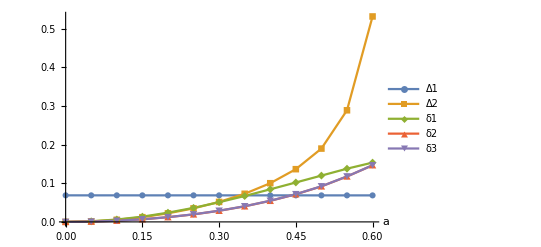

```mathematica
ListLinePlot[Table[{Res[[i,1]],Res[[i,j]]},{j,5,9},{i,1,13}],AxesLabel->{"a",""},PlotLegends->{Δ1,Δ2,δ1,δ2,δ3},PlotRange->All,PlotMarkers->Automatic]
```

```mathematica
Res={{0.2,0.09999999999999999,434.4930507817826,1520.725677736239,0.06872169870885841,0.019159134184026323,0.02085427032689546,0.010520132795654924,0.010632800927540122},{0.2,0.19999999999999998,105.29827109356236,368.5439488274683,0.06872643175098048,0.01947234891278295,0.021175535249759982,0.010694366327924325,0.01080779695253709},{0.2,0.3,44.36090958983947,155.26318356443815,0.06873578271330195,0.01999277274909335,0.0217076963059906,0.010983740625483561,0.011098550699949871},{0.2,0.39999999999999997,23.06184818371316,80.71646864299606,0.0687334422083904,0.020788286017993405,0.02251855816253574,0.011427047668213343,0.011543089037999879},{0.2,0.49999999999999994,13.235022058068404,46.32257720323941,0.06873586814426284,0.022141201139599533,0.023883698272795722,0.012177464936498253,0.012300062554863342},{0.2,0.6,7.929902504522628,27.7546587658292,0.06875229984121894,0.023648005712323745,0.02539468949103516,0.013018167233425165,0.01314223097862737},{0.2,0.7,4.763790218243904,16.673265763853664,0.06874405348182074,0.025326179567683484,0.027068761712560205,0.013962538470245959,0.014079439043299342},{0.2,0.7999999999999999,2.738107560385956,9.583376461350847,0.06872838814437568,0.02968321508499681,0.03130640395596134,0.016396198658306563,0.01651939874822453},{0.2,0.8999999999999999,1.362664027004539,4.769324094515886,0.06874248423397135,0.038522082425395926,0.039541970282731174,0.02134531990702516,0.02146793929441274}}
```

{{0.2,0.1,434.493,1520.73,0.0687217,0.0191591,0.0208543,0.0105201,0.0106328},{0.2,0.2,105.298,368.544,0.0687264,0.0194723,0.0211755,0.0106944,0.0108078},{0.2,0.3,44.3609,155.263,0.0687358,0.0199928,0.0217077,0.0109837,0.0110986},{0.2,0.4,23.0618,80.7165,0.0687334,0.0207883,0.0225186,0.011427,0.0115431},{0.2,0.5,13.235,46.3226,0.0687359,0.0221412,0.0238837,0.0121775,0.0123001},{0.2,0.6,7.9299,27.7547,0.0687523,0.023648,0.0253947,0.0130182,0.0131422},{0.2,0.7,4.76379,16.6733,0.0687441,0.0253262,0.0270688,0.0139625,0.0140794},{0.2,0.8,2.73811,9.58338,0.0687284,0.0296832,0.0313064,0.0163962,0.0165194},{0.2,0.9,1.36266,4.76932,0.0687425,0.0385221,0.039542,0.0213453,0.0214679}}

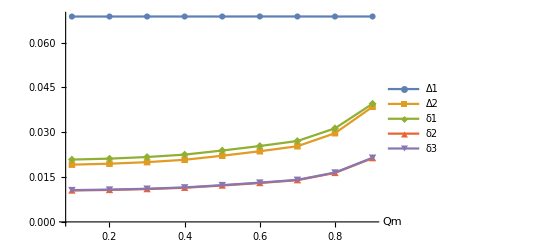

```mathematica
ListLinePlot[Table[{Res[[i,2]],Res[[i,j]]},{j,5,9},{i,1,9}],AxesLabel->{"Qm",""},PlotLegends->{Δ1,Δ2,δ1,δ2,δ3},PlotRange->All,PlotMarkers->Automatic]
```